## Some Fourier Analysis Grant Ovsepyan ECE 533 HW8A

#### There are a bunch of built in sounds in ExampleData. Here is a list:

```mathematica
soundEx=ExampleData["Sound"]
```

{{Sound,AltoFlute},{Sound,AltoFluteScale},{Sound,AltoSaxophone},{Sound,AltoSaxophoneScale},{Sound,Apollo11PhoneCall},{Sound,Apollo11ReturnSafely},{Sound,Apollo11SmallStep},{Sound,Apollo13Countdown},{Sound,Apollo13Problem},{Sound,BalloonPop},{Sound,BassClarinet},{Sound,BassClarinetScale},{Sound,BassFlute},{Sound,BassFluteScale},{Sound,Bassoon},{Sound,BassoonScale},{Sound,BassTrombone},{Sound,BassTromboneScale},{Sound,BlackcapWarbler},{Sound,Burst100},{Sound,Burst1000},{Sound,Burst7350},{Sound,Cello},{Sound,CelloPizzicato},{Sound,CelloPizzicatoScale},{Sound,CelloScale},{Sound,Clarinet},{Sound,ClarinetScale},{Sound,CrashCymbal},{Sound,DoubleBass},{Sound,DoubleBassPizzicato},{Sound,DoubleBassPizzicatoScale},{Sound,DoubleBassScale},{Sound,Flute},{Sound,FluteScale},{Sound,FrenchHorn},{Sound,FrenchHornScale},{Sound,JetSound},{Sound,LinearSweep},{Sound,NoiseBlue},{Sound,NoiseBrown},{Sound,NoisePink},{Sound,NoiseViolet},{Sound,NoiseWhite},{Sound,Oboe},{Sound,OboeScale},{Sound,OrganChord},{Sound,Piano},{Sound,PianoScale},{Sound,RollingCoin},{Sound,SopranoSaxophone},{Sound,SopranoSaxophoneScale},{Sound,Square10},{Sound,Square100},{Sound,Square1000},{Sound,Square7350},{Sound,SubwayTrain},{Sound,TenorTrombone},{Sound,TenorTromboneScale},{Sound,TestIntermodulationDistortion},{Sound,Trumpet},{Sound,TrumpetScale},{Sound,Tuba},{Sound,TubaScale},{Sound,Viola},{Sound,ViolaScale},{Sound,Violin},{Sound,ViolinScale}}

#### Sounds usually import as “Sound Objects” which are displayed like this:

```mathematica
n=1;thisSound=ExampleData[soundEx[[n]]]
```

-Graphics-

```mathematica
thisSound//FullForm
```

Sound[SampledSoundList[List[List[-0.00012207,0.00457778,0.0119938,0.0132145,0.00830103,0.00753807,59163,-0.0146179,-0.0159302,-0.0179749,-0.0174561,-0.0190125,-0.0119324]],22050]]
 |  |  |  |

#### Just as you get the data from an Image Object using ImageData, you get the sound data from a Sound Object using AudioData.

```mathematica
thisData=First@AudioData[thisSound]
```

{-0.00012207,0.00457778,0.0119938,0.0132145,0.00830103,0.00753807,0.00152593,-0.00250244,59160,-0.0107422,-0.0146179,-0.0159302,-0.0179749,-0.0174561,-0.0190125,-0.0119324}
 |  |  |  |

First is used because this is a mono file. If loading a stereo file, you can pick one of the channels, average them together, or work with them separately.

#### The sampling rate is part of the sound object and the duration is easy to calculate.

```mathematica
sr=thisSound[[1,2]]
```

22050

```mathematica
Duration[thisSound]
```

2.68367 s

```mathematica
N[Length[thisData]/sr]
```

2.68367

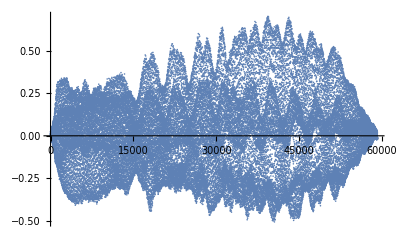

```mathematica
ListPlot[thisData]
```

#### The spectrum of the sound is achieved using the FFT, the discrete version of the Fourier Transform.

```mathematica
Fourier[thisData]
```

{0.340835+3.65116×10^-18 ⅈ,0.00814892+0.000545257 ⅈ,0.00825027-0.000915965 ⅈ,59169,0.00890549+0.000718286 ⅈ,0.00825027+0.000915965 ⅈ,0.00814892-0.000545257 ⅈ}
 |  |  |  |

#### But the raw output of the FFT is a bit hard to parse . Here is one way to organize things:

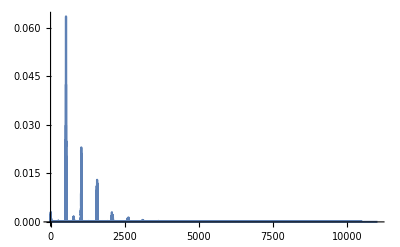

```mathematica
sr=22050;
nfft=Length[thisData];
spec=Abs[Fourier[thisData,FourierParameters->{-1,1}]];
ssf=N[Range[0,sr/2,sr/nfft]];
numDisp=Length[Select[ssf,#<sr/2&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],spec[[1;;numDisp]]}],PlotRange->All]
```

#### We could zoom in and look at just part of the spectrum if desired

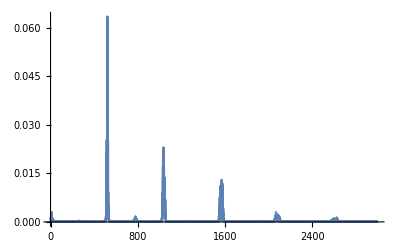

```mathematica
maxFreq=3000;numDisp=Length[Select[ssf,#<maxFreq&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],spec[[1;;numDisp]]}],PlotRange->All]
```

#### It’s common to look at the Log of the spectrum because this agrees (somewhat) with how we perceive things

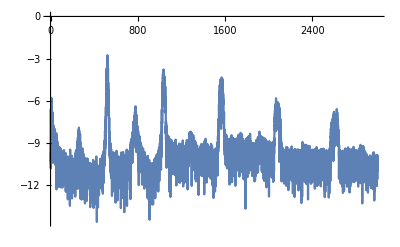

```mathematica
maxFreq=3000;numDisp=Length[Select[ssf,#<maxFreq&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],Log[spec[[1;;numDisp]]]}],PlotRange->All]
```

### Problem 1: Load in one of the sound examples and conduct an analysis of the sound.

```mathematica
(*1a duration of this file*)
soundEx=ExampleData["Sound"];
n=2;thisSound=ExampleData[soundEx[[n]]];
thisSound//FullForm;
Duration[thisSound]
```

14.9403 s

```mathematica
(*q1b: sampling rate of this file *)
sr=thisSound[[1,2]];
```

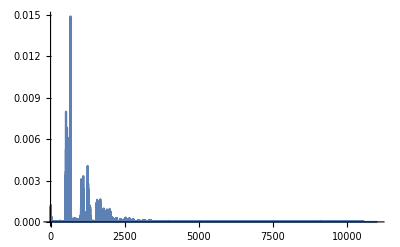

```mathematica
(*q1c highest possible frequency*)
thisData=First@AudioData[thisSound];
nfft=Length[thisData];
spec=Abs[Fourier[thisData,FourierParameters->{-1,1}]];
ssf=N[Range[0,sr/2,sr/nfft]];
numDisp=Length[Select[ssf,#<sr/2&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],spec[[1;;numDisp]]}],PlotRange->All]
```

```mathematica
renderData = spec[[1;;numDisp]]
peaksExtract = PeakDetect[renderData, 250,0,0.0005];
ListPlot[{renderData,renderData peaksExtract}, Joined -> {True,False}, Filling ->{2->0},FillingStyle -> Opacity[1], PlotRange-> All]
```

-Graphics-

Highest possible frequency is around 500.

(d) What are the dominant frequencies present in the sound? (For example, i_(□_□)n the AltoFlute, there are peaks at a bit larger than 500, 1000, 1500, 2000, etc .) . How accurately can you pinpoint these peaks? FindPeaks[] and/or PeakDetect[] may be useful

```mathematica
FindPeaks[renderData, 250,0,0.005]
```

{{8834,0.00608344},{9935,0.0119248}}

The dominant frequencies are 0.00608344  and 0.00608344, which occur at 8834 and 9935.
e) the resolution of the analysis is

```mathematica
sr/Length[spec[[1 ;; numDisp]]] // N
```

```mathematica
(*now repeat for Apollo11SmallStep *)
```

```mathematica
(*duration of this file*)
soundEx=ExampleData["Sound"];
n=7;thisSound=ExampleData[soundEx[[n]]];
thisSound//FullForm;
Duration[thisSound]
```

8.70667 s

```mathematica
(*q1b: sampling rate of this file *)
sr=thisSound[[1,2]];
```

```mathematica
22050
```

22050

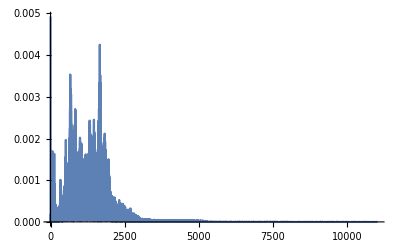

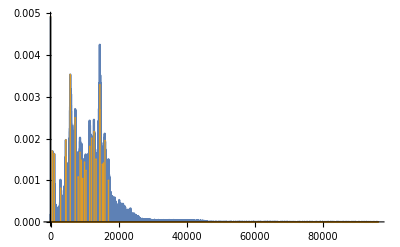

```mathematica
(*q1c highest possible frequency*)
thisData=First@AudioData[thisSound];
nfft=Length[thisData];
spec=Abs[Fourier[thisData,FourierParameters->{-1,1}]];
ssf=N[Range[0,sr/2,sr/nfft]];
numDisp=Length[Select[ssf,#<sr/2&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],spec[[1;;numDisp]]}],PlotRange->All]
renderData = spec[[1;;numDisp]]
peaksExtract = PeakDetect[renderData, 100,0,0.0005];
ListPlot[{renderData,renderData peaksExtract}, Joined -> {True,False}, Filling ->{2->0},FillingStyle -> Opacity[1], PlotRange-> All]
```

Highest possible frequency is around 17000.
(d) What are the dominant frequencies present in the sound? (For example, i_(□_□)n the AltoFlute, there are peaks at a bit larger than 500, 1000, 1500, 2000, etc .) . How accurately can you pinpoint these peaks? FindPeaks[] and/or PeakDetect[] may be useful

```mathematica
FindPeaks[renderData, 250,0,0.002]
```

{{5788,0.00353523},{7232,0.00249914},{12045,0.00200754},{12789,0.00217039},{14479,0.00268556},{14481,0.00328959}}

The dominant frequencies are 00353523  and 00328959, which occur at 5788 and 14481.
  e) the resolution of the analysis is

```mathematica
sr/Length[spec[[1 ;; numDisp]]] // N
```

0.229709

### Problem 2 : Noise Floor

The noise floor is (roughly speaking) the part of the signal that is not part of any peak. So in the AltoFlute sound, this is roughly around the -9dB line. Build a function that can take in the spectrum of a sound and plot out an approximation to the noise floor. For example, below in red is a hand-drawn version of an approximation to the noise floor for the AltoFlute sound.

```mathematica
{-Graphics-}
```

```mathematica
soundEx=ExampleData["Sound"];
n=1;thisSound=ExampleData[soundEx[[n]]];
thisSound//FullForm;
thisData=First@AudioData[thisSound]
sr=thisSound[[1,2]];
sr=22050;
nfft=Length[thisData];
spec=Abs[Fourier[thisData,FourierParameters->{-1,1}]];
ssf=N[Range[0,sr/2,sr/nfft]];
numDisp=Length[Select[ssf,#<sr/2&]];
maxFreq=3000;numDisp=Length[Select[ssf,#<maxFreq&]];
ListLinePlot[Transpose[{ssf[[1;;numDisp]],Log[spec[[1;;numDisp]]]}],PlotRange->All]
```

-Graphics-

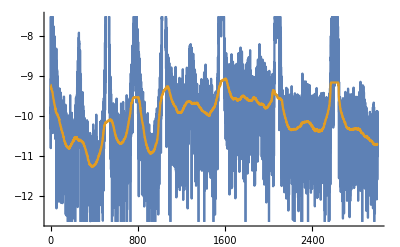

```mathematica
medianArr  = Transpose[{ssf[[1;;numDisp]],Log[MedianFilter[spec[[1;;numDisp]], 200]]}];
data =Transpose[{ssf[[1;;numDisp]],Log[spec[[1;;numDisp]]]}];
ListLinePlot[{data,medianArr}]
```